```mathematica
∇_{x,y,z}^2 Im[Log[x+ⅈ y+c]]//Simplify
```

0

```mathematica
D[D[ArcTan[(y-y0)/(x-x0)], x], x]//Simplify
D[D[ArcTan[(y-y0)/(x-x0)], y], y]//Simplify
```

(2 (x-x0) (y-y0))/((x^2-2 x x0+x0^2+(y-y0)^2)^2)

-(2 (x-x0) (y-y0))/((x^2-2 x x0+x0^2+(y-y0)^2)^2)

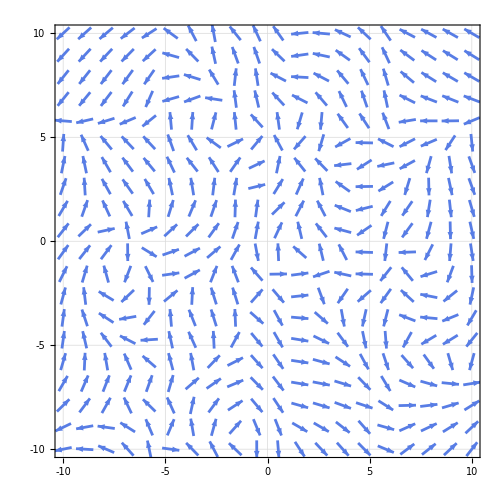

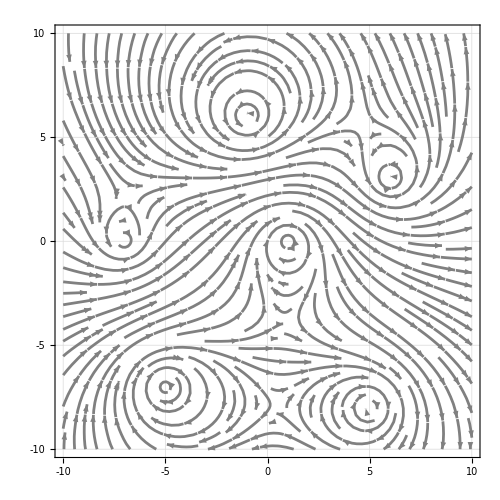

```mathematica
Clear[x,y];
θpositive[n_,x0_,y0_]:=n ArcTan[(y-y0)/(x-x0)];
θnagative[n_,x0_,y0_]:=-n ArcTan[(y-y0)/(x-x0)];
VectorPlot[{(Cos[θpositive[3,6,3]]+Cos[θnagative[3,-5,-7]])+(Cos[θpositive[5,-1,6]]+Cos[θnagative[5,1,0]])+(Cos[θpositive[2,-7,0]]+Cos[θnagative[2,5,-8]]),(Sin[θpositive[3,6,3]]+Sin[θnagative[3,-5,-7]])+(Sin[θpositive[5,-1,6]]+Sin[θnagative[5,1,0]])+(Sin[θpositive[2,-7,0]]+Sin[θnagative[2,5,-8]])},{x,-10,10},{y,-10,10},VectorPoints->20,VectorScale->{0.03,0.85,None},StreamPoints->None,StreamStyle->Gray,PlotRange->{{-10,10},{-10,10}},PlotTheme->"Business",ImageSize->500](*Orientation of Unit Rotors*)
VectorPlot[Evaluate[D[(θpositive[3,6,3]+θnagative[3,-5,-7])+(θpositive[5,-1,6]+θnagative[5,1,0])+(θpositive[2,-7,0]+θnagative[2,5,-8]),{{x,y}}]],{x,-10,10},{y,-10,10},VectorPoints->0,VectorScale->{0.03,0.85,None},StreamPoints->Fine,StreamStyle->Gray,PlotRange->{{-10,10},{-10,10}},PlotTheme->"Business",ImageSize->500]
```

```mathematica
Clear[y];
Sum[ⅇ^(2π ⅈ n x+y n^2),{n,-2,2},Assumptions->y>0]//Simplify
```

1+ⅇ^(-2 ⅈ π x+y)+ⅇ^(2 ⅈ π x+y)+ⅇ^(-4 ⅈ π x+4 y)+ⅇ^(4 ⅈ π x+4 y)

```mathematica
∫_0^(2π) ∫_0^(2π) 1/(4-Cos[kx]-Cos[ky])ⅆkxⅆky
```

(4 π EllipticK[-1/3])/(√3)